```mathematica
Clear[F,G,p,R,Cost];
F[a_,r_,μ_]:=F[a,r,μ]=Piecewise[{{1-∑_(i=0)^(r-1) 1/(i!)*(a/μ)^i*Exp[-a/μ], a>0}, {0, a==0}}];
p[a_,k_,j_,μ_]:=p[a,k,j,μ]=Piecewise[{{Boole[j==1], k==0}, {F[a,k,μ], k≥1&&j==1}, {F[a,k-j+1,μ]-F[a,k-j+2,μ], k≥1&&2≤j&&j≤k}, {1-F[a,1,μ], k≥1&&j==(k+1)}}];
G[a_,r_,μ_]:=G[a,r,μ]=Piecewise[{{μ*r*F[a,r+1,μ]/F[a,r,μ], a>0}, {0, a==0}}];
R[a_,k_,j_,γ_,μ_]:=R[a,k,j,γ,μ]=Piecewise[{{γ*a, (k==0||k==1)}, {(1-γ)*(G[a,k,μ]*(k-1))/2+γ*a, k≥2&&j==1}, {(1-γ)*(a*(j-2)+(G[a,k-(j-1),μ]*(k-(j-2)))/2)+γ*a, k≥2&&2≤j&&j≤k}, {(1-γ)*a*(j-2)+γ*a, k≥2&&j==(k+1)}}];
Cost[a_,n_,k_,γ_,μ_]:=Cost[a,n,k,γ,μ]=∑_(j=1)^(k+1) p[a,k,j,μ]*(R[a,k,j,γ,μ]+OptimalCost[n-1,j,γ,μ]);
```

```mathematica
$Assumptions = {j∈Integers,k∈Integers,a∈Reals,k≥1,j≥1,j≤k+1,a>0};
D[p[a,k,j,1],a]//FullSimplify
D[R[a,k,j,γ,1],a]//FullSimplify
```

Piecewise[{{(a^(-1+k) ⅇ^-a)/Gamma[k], j==1}, {-(a^(-j+k) ⅇ^-a (-1+a+j-k))/Gamma[2-j+k], j≥2&&j≤k}, {-Cosh[a]+Sinh[a], True}}]

Piecewise[{{γ+(a^(-1+k) ⅇ^-a (-1+k) k (-1+γ) Gamma[k] ((-a+k) Gamma[k]+a Gamma[k,a]-Gamma[1+k,a]))/(2 k! (Gamma[k]-Gamma[k,a])^2), j<2||k<2}, {-2+j+3 γ-j γ-(a^(-j+k) ⅇ^-a (-1+γ) Gamma[3-j+k] ((-1+a+j-k) (-j+k)!-a Gamma[1-j+k,a]+Gamma[2-j+k,a]))/(2 Gamma[2-j+k] ((-j+k)!-Gamma[1-j+k,a])^2), j≥2&&j≤k}, {-2+j+3 γ-j γ, True}}]

```mathematica
Clear[PossiblePolicies];
PossiblePolicies[n_,k_,γ_,μ_]:=PossiblePolicies[n,k,γ,μ]=Module[{sol,result},
sol=NSolve[D[Cost[a,n,k,γ,μ],a]==0&&a>0,a]//Quiet;
If[Length[sol]==0,
result={0},
result=Flatten[{0,a/.sol}];
];
result
];
```

```mathematica
Clear[OptimalPolicy];
OptimalPolicy[n_,k_,γ_,μ_]:=OptimalPolicy[n,k,γ,μ]=PossiblePolicies[n,k,γ,μ][[Ordering[Table[Cost[PossiblePolicies[n,k,γ,μ][[i]],n,k,γ,μ],{i,1,Length[PossiblePolicies[n,k,γ,μ]]}],1][[1]]]];
```

```mathematica
Clear[OptimalCost];
OptimalCost[n_,k_,γ_,μ_]:=OptimalCost[n,k,γ,μ]=Piecewise[{{(1-γ)*(μ*k*(k-1))/2+γ*k*μ, n==0}, {Cost[OptimalPolicy[n,k,γ,μ],n,k,γ,μ], n≥1}}];
```

```mathematica
Cost[a,1,1,γ,μ]//FullSimplify
```

Piecewise[{{μ+γ (a+μ), a≤0}, {a γ+(ⅇ^(-a/μ)+γ) μ, True}}]

```mathematica
Limit[Assuming[a>0,FullSimplify[F[a,r,μ]]],a->0]==F[0,r,μ]//FullSimplify
Assuming[r≥1,FullSimplify[Gamma[r,0]==Gamma[r]]]
```

Limit[1-Gamma[r,a/μ]/Gamma[r],a→0]==0

True

```mathematica
μ = 1;
```

```mathematica
Table[Table[OptimalCost[n,0,γ,μ], {γ, 0.05, 0.95, 0.05}], {n, 1, 6}]//MatrixForm
```

(0.05 | 0.1 | 0.15 | 0.2 | 0.25 | 0.3 | 0.35 | 0.4 | 0.45 | 0.5 | 0.55 | 0.6 | 0.65 | 0.7 | 0.75 | 0.8 | 0.85 | 0.9 | 0.95
0.249787 | 0.430259 | 0.584568 | 0.721888 | 0.846574 | 0.961192 | 1.06744 | 1.16652 | 1.25933 | 1.34657 | 1.42881 | 1.5065 | 1.58001 | 1.64967 | 1.71576 | 1.77851 | 1.83814 | 1.89482 | 1.94873
0.448742 | 0.7608 | 1.02291 | 1.25323 | 1.4601 | 1.64827 | 1.82069 | 1.9793 | 2.12544 | 2.26002 | 2.38365 | 2.49671 | 2.59936 | 2.69165 | 2.77341 | 2.84432 | 2.90383 | 2.95104 | 2.9844
0.647606 | 1.09112 | 1.4609 | 1.78405 | 2.07299 | 2.33466 | 2.57334 | 2.79184 | 2.99202 | 3.17509 | 3.3418 | 3.49249 | 3.62716 | 3.74545 | 3.8466 | 3.92931 | 3.99154 | 4.02996 | 4.03848
0.846464 | 1.42143 | 1.89885 | 2.31484 | 2.68583 | 3.02098 | 3.32592 | 3.60429 | 3.85849 | 4.09006 | 4.2999 | 4.48837 | 4.65532 | 4.80009 | 4.92136 | 5.01698 | 5.0834 | 5.11469 | 5.09928
1.04532 | 1.75174 | 2.33681 | 2.84563 | 3.29867 | 3.7073 | 4.07849 | 4.41673 | 4.72496 | 5.00503 | 5.258 | 5.48425 | 5.6835 | 5.85478 | 5.99629 | 6.10502 | 6.17603 | 6.20082 | 6.16228)

```mathematica
output = "[";
For[n=1,n≤5,n++,
For[γ=0.05,γ≤0.9,γ+=0.05,
output = StringJoin[{output,ToString[OptimalCost[n,0,γ,μ]],", "}]];
output = StringJoin[{output, ToString[OptimalCost[n, 0, 0.95, μ]], "; "}]];
For[γ=0.05,γ≤0.9,γ+=0.05,
output=StringJoin[{output, ToString[OptimalCost[6,0,γ,μ]], ", "}]];
output = StringJoin[{output, ToString[OptimalCost[6,0,0.95,μ]], "]"}];
Print[output]
```

[0.05, 0.1, 0.15, 0.2, 0.25, 0.3, 0.35, 0.4, 0.45, 0.5, 0.55, 0.6, 0.65, 0.7, 0.75, 0.8, 0.85, 0.9, 0.95; 0.249787, 0.430259, 0.584568, 0.721888, 0.846574, 0.961192, 1.06744, 1.16652, 1.25933, 1.34657, 1.42881, 1.5065, 1.58001, 1.64967, 1.71576, 1.77851, 1.83814, 1.89482, 1.94873; 0.448742, 0.7608, 1.02291, 1.25323, 1.4601, 1.64827, 1.82069, 1.9793, 2.12544, 2.26002, 2.38365, 2.49671, 2.59936, 2.69165, 2.77341, 2.84432, 2.90383, 2.95104, 2.9844; 0.647606, 1.09112, 1.4609, 1.78405, 2.07299, 2.33466, 2.57334, 2.79184, 2.99202, 3.17509, 3.3418, 3.49249, 3.62716, 3.74545, 3.8466, 3.92931, 3.99154, 4.02996, 4.03848; 0.846464, 1.42143, 1.89885, 2.31484, 2.68583, 3.02098, 3.32592, 3.60429, 3.85849, 4.09006, 4.2999, 4.48837, 4.65532, 4.80009, 4.92136, 5.01698, 5.0834, 5.11469, 5.09928; 1.04532, 1.75174, 2.33681, 2.84563, 3.29867, 3.7073, 4.07849, 4.41673, 4.72496, 5.00503, 5.258, 5.48425, 5.6835, 5.85478, 5.99629, 6.10502, 6.17603, 6.20082, 6.16228]

```mathematica
μ=1;
γ=0.5;
```

```mathematica
OptimalPolicy[1,1,γ,μ]==-μ*Log[γ]
```

True

```mathematica
num=6;
Table[OptimalCost[n,0,γ,μ],{n,0,num}]
Table[Table[If[n+k≤num,OptimalCost[n,k,γ,μ],0],{k,0,num}],{n,0,num}]//MatrixForm
Table[Table[If[n+k≤num,OptimalPolicy[n,k,γ,μ],0],{k,0,num}],{n,1,num}]//MatrixForm
```

{0.,0.5,1.34657,2.26002,3.17509,4.09006,5.00503}

(0. | 0.5 | 1.5 | 3. | 5. | 7.5 | 10.5
0.5 | 1.34657 | 2.48969 | 4.02475 | 5.98026 | 8.37089 | 0
1.34657 | 2.26002 | 3.40683 | 4.94061 | 6.89375 | 0 | 0
2.26002 | 3.17509 | 4.32169 | 5.85527 | 0 | 0 | 0
3.17509 | 4.09006 | 5.23664 | 0 | 0 | 0 | 0
4.09006 | 5.00503 | 0 | 0 | 0 | 0 | 0
5.00503 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0.693147 | 1.75711 | 2.82577 | 3.85505 | 4.8492 | 0
0 | 0.826902 | 1.90223 | 2.95223 | 3.95872 | 0 | 0
0 | 0.83013 | 1.90481 | 2.95403 | 0 | 0 | 0
0 | 0.82995 | 1.90455 | 0 | 0 | 0 | 0
0 | 0.829925 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
TeXForm[MatrixForm[Table[Table[If[n+k≤num,OptimalCost[n,k,γ,μ],0],{k,0,num}],{n,0,num}]]]
```

\left(
\begin{array}{ccccccc}
 0. & 0.5 & 1.5 & 3. & 5. & 7.5 & 10.5 \\
 0.5 & 1.34657 & 2.48969 & 4.02475 & 5.98026 & 8.37089 & 0 \\
 1.34657 & 2.26002 & 3.40683 & 4.94061 & 6.89375 & 0 & 0 \\
 2.26002 & 3.17509 & 4.32169 & 5.85527 & 0 & 0 & 0 \\
 3.17509 & 4.09006 & 5.23664 & 0 & 0 & 0 & 0 \\
 4.09006 & 5.00503 & 0 & 0 & 0 & 0 & 0 \\
 5.00503 & 0 & 0 & 0 & 0 & 0 & 0 \\
\end{array}
\right)

```mathematica
TeXForm[MatrixForm[Table[Table[If[n+k≤num,OptimalPolicy[n,k,γ,μ],0],{k,0,num}],{n,1,num}]]]
```

\left(
\begin{array}{ccccccc}
 0 & 0.693147 & 1.75711 & 2.82577 & 3.85505 & 4.8492 & 0 \\
 0 & 0.826902 & 1.90223 & 2.95223 & 3.95872 & 0 & 0 \\
 0 & 0.83013 & 1.90481 & 2.95403 & 0 & 0 & 0 \\
 0 & 0.82995 & 1.90455 & 0 & 0 & 0 & 0 \\
 0 & 0.829925 & 0 & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
\end{array}
\right)

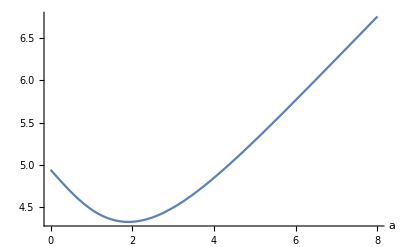

```mathematica
Plot[Cost[a,3,2,γ,μ],{a,0,8},AxesLabel->Automatic]
```

```mathematica
Cost[a,3,2,γ,μ]//FullSimplify
```

Piecewise[{{4.94061+1. a, a≤0}, {2.76002+0.5 a+(2.18058+(1.64681+0.25 a) a) ⅇ^-a-(0.5 a^2)/(-1.+1. ⅇ^a), True}}]

```mathematica
Cost[0,3,2,γ,μ]==Limit[Cost[a,3,2,γ,μ],a->0]
```

True

```mathematica
Assuming[a>0,Cost[a,3,2,γ,μ]//FullSimplify]
```

2.76002+0.5 a+(2.18058+(1.64681+0.25 a) a) ⅇ^-a-(0.5 a^2)/(-1.+1. ⅇ^a)

```mathematica
TeXForm[Assuming[a>0,Cost[a,3,2,γ,μ]//FullSimplify]]
```

-\frac{0.5 a^2}{1. e^a-1.}+0.5 a+((0.25 a+1.64681) a+2.18058) e^{-a}+2.76002

```mathematica
PossiblePolicies[3,2,γ,μ]
OptimalPolicy[3,2,γ,μ]
OptimalCost[3,2,γ,μ]
```

{0,1.90481}

1.90481

4.32169